General::munfl: Exp[-715.52] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-716.39] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-716.389] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

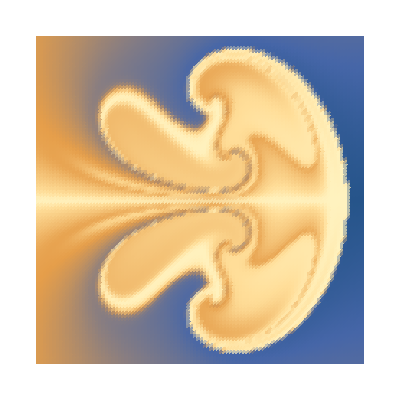

```mathematica
(*runtime:21 seconds,increase n for better resolution*)n=100;tmax=0.85;dt=tmax/100;rcore=0.1;Klist={1,-1,1,-1};zlist={-1-0.5I,-1+0.5I,-0.5-0.5I,-0.5+0.5I};m=Length[zlist];
v[K_,z_,z0_]:=Module[{r2=Abs[z-z0]^2},I K(z0-z)/r2(1-Exp[-r2/rcore^2])];
Runge[z_]:=Module[{},k1=dt vtot[z];k2=dt vtot[z+k1/2];k3=dt vtot[z+k2/2];k4=dt vtot[z+k3];(k1+2 k2+2 k3+k4)/6];
vtot[zlist_]:=Table[Sum[If[i==j,0,v[Klist[[j]],zlist[[i]],zlist[[j]]]],{j,1,m}],{i,1,m}];zlists=Transpose[Table[zlist+=Runge[zlist],{t,0,tmax,dt}]];
vtot[z_]:=Plus@@v[Klist,z,zlists[[All,t]]];image=Table[z=x+I y;Do[z-=Runge[z],{t,100,1,-1}];z,{y,-1.125,1.125,2.25/n},{x,-0.35,1.9,2.25/n}];
ListDensityPlot[Map[Sign[Im[#]]Arg[#]&,image,{2}],Mesh->False,Frame->False,AspectRatio->Automatic]
```

```mathematica
ListDensityPlot[Map[Sign[Im[#]]Arg[#]&,image,{2}],Mesh->False,Frame->False,AspectRatio->Automatic]
```

-Graphics-

```mathematica
Dimensions[image]
```

{24,24}

```mathematica
Dimensions[Map[Sign[Im[#]]Arg[#]&,image,{2}]]
```

{24,24}

```mathematica
Map[Sign[Im[#]]Arg[#]&,image,{2}]
Map[Sign[Im[#]]Arg[#]&,image,{1}]
```

{{1.48339,1.38552,1.28273,1.17646,1.07121,0.973345,0.887474,0.813418,0.74666,0.681213,0.612255,0.538614,0.465711,0.405658,0.36921,0.356806,0.361092,0.373317,0.386988,0.398647,0.406977,0.411806,0.413477,0.412508},{1.47799,1.37314,1.25955,1.13867,1.0181,0.909717,0.821351,0.750037,0.685942,0.618413,0.537381,0.436378,0.333493,3.01824,3.1254,3.10744,0.276171,0.270801,0.301571,0.327649,0.346464,0.358793,0.365882,0.368908},{1.47991,1.36908,1.24366,1.10421,0.96337,0.845015,0.761897,0.698286,0.637082,0.567048,0.46892,0.34792,2.10498,1.894,1.95,2.39421,2.76157,3.02213,0.22581,0.252723,0.283833,0.304814,0.317844,0.325063},{1.49157,1.37744,1.24079,1.07885,0.91218,0.804471,0.788215,0.716048,0.617036,0.534775,0.42264,2.74595,1.81388,2.06359,2.26077,2.26319,2.24863,2.95704,2.86562,0.204775,0.221473,0.251152,0.270255,0.281607},{1.51466,1.40232,1.25881,1.07333,0.878976,1.40204,3.00435,2.73649,0.791505,0.536041,0.421808,2.75282,1.78174,1.74373,2.62908,2.72311,2.62053,2.53614,2.95401,2.93393,0.171415,0.199717,0.224199,0.239255},{1.54932,1.44621,1.30584,1.10504,0.883764,3.10542,2.20895,2.66881,3.0642,0.777278,0.467387,0.432291,3.0885,2.98899,2.71856,2.8361,2.83912,2.77276,2.82063,3.01713,3.12977,0.153884,0.180883,0.198731},{1.5942,1.50913,1.38556,1.19275,0.918059,2.14687,2.18388,2.18905,2.38492,3.09754,1.13846,0.530295,1.95425,2.62091,2.80775,2.86361,2.90055,2.8914,2.86576,2.97863,2.98378,0.128506,0.141521,0.160681},{1.64932,1.59091,1.4991,1.33684,1.06965,2.63837,2.23684,2.27291,2.24566,2.38549,3.12595,3.00311,3.11515,2.20597,2.81525,2.1583,2.36306,2.92406,2.92954,2.95899,3.08741,3.1206,0.107205,0.125562},{1.7718,1.65557,1.68293,1.54329,1.33091,0.994861,2.18716,2.33423,2.34328,2.30817,2.401,3.09561,3.09028,2.08042,1.1353,2.79549,2.07379,1.84806,2.93378,2.96841,2.70238,3.07902,0.078748,0.0935419},{2.08414,1.8577,1.68017,2.01703,1.80833,1.44127,1.09878,2.19336,2.39322,2.41166,2.376,2.40454,2.69681,2.58951,2.45581,1.36184,2.14505,2.36834,1.98534,2.81909,2.44496,3.06586,0.0563565,0.0644262},{2.45747,2.33212,2.16683,1.92743,1.69611,2.60985,2.36385,1.53728,1.11214,2.25817,2.46022,2.46622,2.43564,2.44349,2.51912,2.0281,2.34157,2.65868,2.50528,2.29402,2.56927,3.10894,0.0382672,0.0376534},{2.90096,2.84954,2.78493,2.70421,2.60572,2.49032,2.35311,2.16429,1.86651,2.23853,2.76811,2.54528,1.72875,1.78953,2.77933,2.22748,2.82261,2.97982,2.93649,2.84902,2.934,3.1331,0.0159862,0.0123805},{2.90096,2.84954,2.78493,2.70421,2.60572,2.49032,2.35311,2.16429,1.86651,2.23853,2.76811,2.54528,1.72875,1.78953,2.77933,2.22748,2.82261,2.97982,2.93649,2.84902,2.934,3.1331,0.0159862,0.0123805},{2.45747,2.33212,2.16683,1.92743,1.69611,2.60985,2.36385,1.53728,1.11214,2.25817,2.46022,2.46622,2.43564,2.44349,2.51912,2.0281,2.34157,2.65868,2.50528,2.29402,2.56927,3.10894,0.0382672,0.0376534},{2.08414,1.8577,1.68017,2.01703,1.80833,1.44127,1.09878,2.19336,2.39322,2.41166,2.376,2.40454,2.69681,2.58951,2.45581,1.36184,2.14505,2.36834,1.98534,2.81909,2.44496,3.06586,0.0563565,0.0644262},{1.7718,1.65557,1.68293,1.54329,1.33091,0.994861,2.18716,2.33423,2.34328,2.30817,2.401,3.09561,3.09028,2.08042,1.1353,2.79549,2.07379,1.84806,2.93378,2.96841,2.70238,3.07902,0.078748,0.0935419},{1.64932,1.59091,1.4991,1.33684,1.06965,2.63837,2.23684,2.27291,2.24566,2.38549,3.12595,3.00311,3.11515,2.20597,2.81525,2.1583,2.36306,2.92406,2.92954,2.95899,3.08741,3.1206,0.107205,0.125562},{1.5942,1.50913,1.38556,1.19275,0.918059,2.14687,2.18388,2.18905,2.38492,3.09754,1.13846,0.530295,1.95425,2.62091,2.80775,2.86361,2.90055,2.8914,2.86576,2.97863,2.98378,0.128506,0.141521,0.160681},{1.54932,1.44621,1.30584,1.10504,0.883764,3.10542,2.20895,2.66881,3.0642,0.777278,0.467387,0.432291,3.0885,2.98899,2.71856,2.8361,2.83912,2.77276,2.82063,3.01713,3.12977,0.153884,0.180883,0.198731},{1.51466,1.40232,1.25881,1.07333,0.878976,1.40204,3.00435,2.73649,0.791505,0.536041,0.421808,2.75282,1.78174,1.74373,2.62908,2.72311,2.62053,2.53614,2.95401,2.93393,0.171415,0.199717,0.224199,0.239255},{1.49157,1.37744,1.24079,1.07885,0.91218,0.804471,0.788215,0.716048,0.617036,0.534775,0.42264,2.74595,1.81388,2.06359,2.26077,2.26319,2.24863,2.95704,2.86562,0.204775,0.221473,0.251152,0.270255,0.281607},{1.47991,1.36908,1.24366,1.10421,0.96337,0.845015,0.761897,0.698286,0.637082,0.567048,0.46892,0.34792,2.10498,1.894,1.95,2.39421,2.76157,3.02213,0.22581,0.252723,0.283833,0.304814,0.317844,0.325063},{1.47799,1.37314,1.25955,1.13867,1.0181,0.909717,0.821351,0.750037,0.685942,0.618413,0.537381,0.436378,0.333493,3.01824,3.1254,3.10744,0.276171,0.270801,0.301571,0.327649,0.346464,0.358793,0.365882,0.368908},{1.48339,1.38552,1.28273,1.17646,1.07121,0.973345,0.887474,0.813418,0.74666,0.681213,0.612255,0.538614,0.465711,0.405658,0.36921,0.356806,0.361092,0.373317,0.386988,0.398647,0.406977,0.411806,0.413477,0.412508}}

{{1.48339,1.38552,1.28273,1.17646,1.07121,0.973345,0.887474,0.813418,0.74666,0.681213,0.612255,0.538614,0.465711,0.405658,0.36921,0.356806,0.361092,0.373317,0.386988,0.398647,0.406977,0.411806,0.413477,0.412508},{1.47799,1.37314,1.25955,1.13867,1.0181,0.909717,0.821351,0.750037,0.685942,0.618413,0.537381,0.436378,0.333493,3.01824,3.1254,3.10744,0.276171,0.270801,0.301571,0.327649,0.346464,0.358793,0.365882,0.368908},{1.47991,1.36908,1.24366,1.10421,0.96337,0.845015,0.761897,0.698286,0.637082,0.567048,0.46892,0.34792,2.10498,1.894,1.95,2.39421,2.76157,3.02213,0.22581,0.252723,0.283833,0.304814,0.317844,0.325063},{1.49157,1.37744,1.24079,1.07885,0.91218,0.804471,0.788215,0.716048,0.617036,0.534775,0.42264,2.74595,1.81388,2.06359,2.26077,2.26319,2.24863,2.95704,2.86562,0.204775,0.221473,0.251152,0.270255,0.281607},{1.51466,1.40232,1.25881,1.07333,0.878976,1.40204,3.00435,2.73649,0.791505,0.536041,0.421808,2.75282,1.78174,1.74373,2.62908,2.72311,2.62053,2.53614,2.95401,2.93393,0.171415,0.199717,0.224199,0.239255},{1.54932,1.44621,1.30584,1.10504,0.883764,3.10542,2.20895,2.66881,3.0642,0.777278,0.467387,0.432291,3.0885,2.98899,2.71856,2.8361,2.83912,2.77276,2.82063,3.01713,3.12977,0.153884,0.180883,0.198731},{1.5942,1.50913,1.38556,1.19275,0.918059,2.14687,2.18388,2.18905,2.38492,3.09754,1.13846,0.530295,1.95425,2.62091,2.80775,2.86361,2.90055,2.8914,2.86576,2.97863,2.98378,0.128506,0.141521,0.160681},{1.64932,1.59091,1.4991,1.33684,1.06965,2.63837,2.23684,2.27291,2.24566,2.38549,3.12595,3.00311,3.11515,2.20597,2.81525,2.1583,2.36306,2.92406,2.92954,2.95899,3.08741,3.1206,0.107205,0.125562},{1.7718,1.65557,1.68293,1.54329,1.33091,0.994861,2.18716,2.33423,2.34328,2.30817,2.401,3.09561,3.09028,2.08042,1.1353,2.79549,2.07379,1.84806,2.93378,2.96841,2.70238,3.07902,0.078748,0.0935419},{2.08414,1.8577,1.68017,2.01703,1.80833,1.44127,1.09878,2.19336,2.39322,2.41166,2.376,2.40454,2.69681,2.58951,2.45581,1.36184,2.14505,2.36834,1.98534,2.81909,2.44496,3.06586,0.0563565,0.0644262},{2.45747,2.33212,2.16683,1.92743,1.69611,2.60985,2.36385,1.53728,1.11214,2.25817,2.46022,2.46622,2.43564,2.44349,2.51912,2.0281,2.34157,2.65868,2.50528,2.29402,2.56927,3.10894,0.0382672,0.0376534},{2.90096,2.84954,2.78493,2.70421,2.60572,2.49032,2.35311,2.16429,1.86651,2.23853,2.76811,2.54528,1.72875,1.78953,2.77933,2.22748,2.82261,2.97982,2.93649,2.84902,2.934,3.1331,0.0159862,0.0123805},{2.90096,2.84954,2.78493,2.70421,2.60572,2.49032,2.35311,2.16429,1.86651,2.23853,2.76811,2.54528,1.72875,1.78953,2.77933,2.22748,2.82261,2.97982,2.93649,2.84902,2.934,3.1331,0.0159862,0.0123805},{2.45747,2.33212,2.16683,1.92743,1.69611,2.60985,2.36385,1.53728,1.11214,2.25817,2.46022,2.46622,2.43564,2.44349,2.51912,2.0281,2.34157,2.65868,2.50528,2.29402,2.56927,3.10894,0.0382672,0.0376534},{2.08414,1.8577,1.68017,2.01703,1.80833,1.44127,1.09878,2.19336,2.39322,2.41166,2.376,2.40454,2.69681,2.58951,2.45581,1.36184,2.14505,2.36834,1.98534,2.81909,2.44496,3.06586,0.0563565,0.0644262},{1.7718,1.65557,1.68293,1.54329,1.33091,0.994861,2.18716,2.33423,2.34328,2.30817,2.401,3.09561,3.09028,2.08042,1.1353,2.79549,2.07379,1.84806,2.93378,2.96841,2.70238,3.07902,0.078748,0.0935419},{1.64932,1.59091,1.4991,1.33684,1.06965,2.63837,2.23684,2.27291,2.24566,2.38549,3.12595,3.00311,3.11515,2.20597,2.81525,2.1583,2.36306,2.92406,2.92954,2.95899,3.08741,3.1206,0.107205,0.125562},{1.5942,1.50913,1.38556,1.19275,0.918059,2.14687,2.18388,2.18905,2.38492,3.09754,1.13846,0.530295,1.95425,2.62091,2.80775,2.86361,2.90055,2.8914,2.86576,2.97863,2.98378,0.128506,0.141521,0.160681},{1.54932,1.44621,1.30584,1.10504,0.883764,3.10542,2.20895,2.66881,3.0642,0.777278,0.467387,0.432291,3.0885,2.98899,2.71856,2.8361,2.83912,2.77276,2.82063,3.01713,3.12977,0.153884,0.180883,0.198731},{1.51466,1.40232,1.25881,1.07333,0.878976,1.40204,3.00435,2.73649,0.791505,0.536041,0.421808,2.75282,1.78174,1.74373,2.62908,2.72311,2.62053,2.53614,2.95401,2.93393,0.171415,0.199717,0.224199,0.239255},{1.49157,1.37744,1.24079,1.07885,0.91218,0.804471,0.788215,0.716048,0.617036,0.534775,0.42264,2.74595,1.81388,2.06359,2.26077,2.26319,2.24863,2.95704,2.86562,0.204775,0.221473,0.251152,0.270255,0.281607},{1.47991,1.36908,1.24366,1.10421,0.96337,0.845015,0.761897,0.698286,0.637082,0.567048,0.46892,0.34792,2.10498,1.894,1.95,2.39421,2.76157,3.02213,0.22581,0.252723,0.283833,0.304814,0.317844,0.325063},{1.47799,1.37314,1.25955,1.13867,1.0181,0.909717,0.821351,0.750037,0.685942,0.618413,0.537381,0.436378,0.333493,3.01824,3.1254,3.10744,0.276171,0.270801,0.301571,0.327649,0.346464,0.358793,0.365882,0.368908},{1.48339,1.38552,1.28273,1.17646,1.07121,0.973345,0.887474,0.813418,0.74666,0.681213,0.612255,0.538614,0.465711,0.405658,0.36921,0.356806,0.361092,0.373317,0.386988,0.398647,0.406977,0.411806,0.413477,0.412508}}

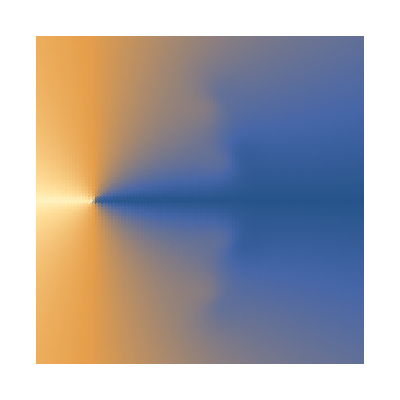

```mathematica
image=Table[z=x+I y;Do[z-=Runge[z],{t,100,98,-1}];z,{y,-1.125,1.125,2.25/n},{x,-0.35,1.9,2.25/n}];
ListDensityPlot[Map[Sign[Im[#]]Arg[#]&,image,{2}],Mesh->False,Frame->False,AspectRatio->Automatic]
```

```mathematica
Dimensions[Table[z=x+I y;z,{y,-1.125,1.125,2.25/n},{x,-0.35,1.9,2.25/n}]]
```

{101,101}